# PHAS2443: Practical Mathematics II Exercises 5: Elliptic Differential Equations

1. This question asks you to automate the process of running an over-relaxation process for solving Laplace's equation on a square mesh. Note that we can express the update rule as
  ϕ_(i,j) = ϕ_(i,j)+w(ϕ_(i+1,j)+ϕ_(i-1,j)+ϕ_(i,j+1)+ϕ_(i,j-1)-4 ϕ_(i,j))/4
        = (1-w) ϕ_(i,j)+w(ϕ_(i+1,j)+ϕ_(i-1,j)+ϕ_(i,j+1)+ϕ_(i,j-1))/4
  so that we can very simply sweep through the mesh. In fact the easiest way to do this is to set up the whole mesh, including the boundaries, but only update the interior points.
    Note that because of the way the over-relaxation algorithm works, one updates points one by one, rather than updating the whole mesh at once -- this is a case where it is NOT appropriate to use the Rotate.. functions.   
     Set up Mathematica code to apply this scheme to a general mesh, N by M.  The suggested approach is to write a function which will make one pass through the whole mesh, and then to Nest that. Solve the same problem as we looked at in the lectures, with the top and bottom of a plate held at 400K and the sides at 300K, for the cases:
     i) N=20, M=20;
     ii) N=10, M=40.
     In each case find out how many iterations are required for the process to converge to 0.01K (which suggests that NestWhile might be useful), 
      a) with no over-relaxation (w=1)
      b) with the over-relaxation factor set to 1.05.

2. In Lecture 4 (more specifically, in the exercises that went with Lecture 4) we saw that the detailed way in which we set up the difference scheme was important, in terms of ensuring that the difference equations converged, in the limit, to the right differential equations.

  This exercise looks at the problems of setting up a scheme in polar coordinates. Consider the following r-θ mesh:

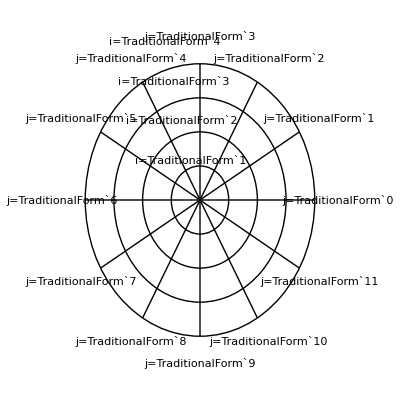

```mathematica
Show[Graphics[Flatten[{Table[{Line[{{0,0},{Cos[2π j/12],Sin[2π j/12]}}],Text[StringForm["j=``",j],1.2{Cos[2π j/12],Sin[2π j/12]}]},{j,0,11}],Table[{Circle[{0,0},i/4.],Text[StringForm["i=``",i],1.2 i{Cos[2π 3.5/12],Sin[2π 3.5/12]}/4]},{i,1,4}]}]],AspectRatio->Automatic]
```

Now let's set up and solve Laplace's equation on this mesh. In polar coordinates we can write
 (1) ∇^2 = 1/r ∂/(∂r)(r ∂/(∂r)) + 1/r^2 ∂^2/(∂θ^2)
 or
 (2) ∇^2 = ∂^2/(∂r^2) +1/r ∂/(∂r) + 1/r^2 ∂^2/(∂θ^2).
  Express both (1) and (2) in finite difference form for a problem with axial symmetry (that is, assuming no variation with θ). Are they the same?
    Hence solve, on the mesh similar to the one illustrated above, the problem of steady-state heat flow through the lagging of a pipe when the pipe, of external radius 0.05m, is at 500K and the outside of the lagging, of radius 0.1m, is held at 300K. Use a mesh with 11 radial points, so that θ_1= 500 and θ_11=300. Note that we have reduced the problem to a one-dimensional one, in r only. You may use the Gauss-Seidel method or a matrix method.
  Compare your results with the exact solution, θ(r) = A ln(r)+B.

A.H. Harker
Physics and Astronomy, UCL
September 2005